```mathematica
(*Keep the bettor indifferent between bluffing any amount and checking at the max bluffing hand strength*)bluffIndiff=c[s]+(1-c[s]) (-s)==x2

(*Keep the caller indifferent between calling and folding to a bet (between min and max)*)
callIndiff=b'[s] (1+s)-v'[s] (-s)==0

(*Keep the caller indifferent between calling and folding to an All-in*)
callIndiffMax=x0 (1+U)+(1-x5) (-U)==0

(*Keep the caller indifferent between calling and folding to a min bet*)
callIndiffMin=(x2-x1) (1+L)+(x4-x3) (-L)==0

(*The size that the bettor uses for a value bet must maximize EV*)
(*This comes from differentiating the EV of bet return WRT s and setting to 0*)
valueOptimality=-s*c'[s]-c[s]+2 v[s]-1==0

(*The boundary points of the bluffing function and value function*)
boundaryConditions={b[U]==x0,b[L]==x1,v[U]==x5,v[L]==x4}

(*Keep the bettor indifferent between checking and making a min value bet with the most marginal value betting hand*)
valueIndiff=c[L]+(1+L) (x3-c[L])+(1-x3) (-L)==x3
```

-s (1-c[s])+c[s]==x2

(1+s) b'[s]+s v'[s]==0

(1+U) x0-U (1-x5)==0

(1+L) (-x1+x2)-L (-x3+x4)==0

-1-c[s]+2 v[s]-s c'[s]==0

{b[U]==x0,b[L]==x1,v[U]==x5,v[L]==x4}

-L (1-x3)+(1+L) (x3-c[L])+c[L]==x3

```mathematica
(*Solve for c(s) first*)
Csol=Solve[{bluffIndiff},{c[s]}][[1]]
(*
Use c(s) to solve for v(s)*)
Vsol=Solve[{valueOptimality/. {c'[s]->D[c[s]/. Csol,s]}/. Csol},{v[s]}][[1]]

(*Use v(s) to solve for b(s),getting an extra constant of integration C1*)
Bsol=DSolve[{callIndiff/. {v'[s]->D[v[s]/. Vsol/. Csol,s]}},b[s],s,GeneratedParameters->(C1&)][[1]]

Union[{callIndiffMax,callIndiffMin,valueIndiff},boundaryConditions]/. {b[s_]->b[s]/. Bsol}/. {v[s_]->v[s]/. Vsol}/. {c[s_]->c[s]/. Csol};

(*Use v(s),c(s),and b(s) with all our equations to solve for all the scalars*)
Xsol=Solve[Union[{callIndiffMax,callIndiffMin,valueIndiff},boundaryConditions]/. {b[s_]->b[s]/. Bsol}/. {v[s_]->v[s]/. Vsol}/. {c[s_]->c[s]/. Csol},{x0,x1,x2,x3,x4,x5,C1}][[1]]//Simplify

(*Plug the scalars back into the function solutions*)
LimitSol=Union[Vsol/. Xsol,Csol/. Xsol,Bsol/. Xsol,Xsol]//Simplify;
```

{c[s]→(s+x2)/(1+s)}

{v[s]→(1+4 s+2 s^2+x2)/(2 (1+s)^2)}

{b[s]→C1-((1+3 s) (-1+x2))/(6 (1+s)^3)}

{x0→(3 (1+L)^3 U)/(6+21 U+21 U^2+7 U^3+L^3 (5+18 U+18 U^2+6 U^3)+3 L (6+21 U+21 U^2+7 U^3)+3 L^2 (6+21 U+21 U^2+7 U^3)),x1→(-3 L^2-L^3+U (3+3 U+U^2)+3 L U (3+3 U+U^2))/(6+21 U+21 U^2+7 U^3+L^3 (5+18 U+18 U^2+6 U^3)+3 L (6+21 U+21 U^2+7 U^3)+3 L^2 (6+21 U+21 U^2+7 U^3)),x2→(-L^3+U (3+3 U+U^2)+3 L U (3+3 U+U^2)+3 L^2 U (3+3 U+U^2))/(6+21 U+21 U^2+7 U^3+L^3 (5+18 U+18 U^2+6 U^3)+3 L (6+21 U+21 U^2+7 U^3)+3 L^2 (6+21 U+21 U^2+7 U^3)),x3→(3+12 U+12 U^2+4 U^3+3 L (4+15 U+15 U^2+5 U^3)+3 L^2 (5+18 U+18 U^2+6 U^3)+L^3 (5+18 U+18 U^2+6 U^3))/(6+21 U+21 U^2+7 U^3+L^3 (5+18 U+18 U^2+6 U^3)+3 L (6+21 U+21 U^2+7 U^3)+3 L^2 (6+21 U+21 U^2+7 U^3)),x4→(3+12 U+12 U^2+4 U^3+3 L (5+18 U+18 U^2+6 U^3)+L^3 (5+18 U+18 U^2+6 U^3)+3 L^2 (6+21 U+21 U^2+7 U^3))/(6+21 U+21 U^2+7 U^3+L^3 (5+18 U+18 U^2+6 U^3)+3 L (6+21 U+21 U^2+7 U^3)+3 L^2 (6+21 U+21 U^2+7 U^3)),x5→(3+18 U+21 U^2+7 U^3+L^3 (2+15 U+18 U^2+6 U^3)+3 L (3+18 U+21 U^2+7 U^3)+3 L^2 (3+18 U+21 U^2+7 U^3))/(6+21 U+21 U^2+7 U^3+L^3 (5+18 U+18 U^2+6 U^3)+3 L (6+21 U+21 U^2+7 U^3)+3 L^2 (6+21 U+21 U^2+7 U^3)),C1→-(1+L)^3/(6+21 U+21 U^2+7 U^3+L^3 (5+18 U+18 U^2+6 U^3)+3 L (6+21 U+21 U^2+7 U^3)+3 L^2 (6+21 U+21 U^2+7 U^3))}

```mathematica
(*define the final functions b,c,and v*)
b[s_,L_,U_]=(b[s]/. LimitSol)
c[s_,L_,U_]=(c[s]/. LimitSol)
v[s_,L_,U_]=(v[s]/. LimitSol)
```

-((1+L)^3 (3 s^2+s^3-U (3+3 U+U^2)-3 s U (3+3 U+U^2)))/((1+s)^3 (6+21 U+21 U^2+7 U^3+L^3 (5+18 U+18 U^2+6 U^3)+3 L (6+21 U+21 U^2+7 U^3)+3 L^2 (6+21 U+21 U^2+7 U^3)))

(s+(-L^3+U (3+3 U+U^2)+3 L U (3+3 U+U^2)+3 L^2 U (3+3 U+U^2))/(6+21 U+21 U^2+7 U^3+L^3 (5+18 U+18 U^2+6 U^3)+3 L (6+21 U+21 U^2+7 U^3)+3 L^2 (6+21 U+21 U^2+7 U^3)))/(1+s)

(1+4 s+2 s^2+(-L^3+U (3+3 U+U^2)+3 L U (3+3 U+U^2)+3 L^2 U (3+3 U+U^2))/(6+21 U+21 U^2+7 U^3+L^3 (5+18 U+18 U^2+6 U^3)+3 L (6+21 U+21 U^2+7 U^3)+3 L^2 (6+21 U+21 U^2+7 U^3)))/(2 (1+s)^2)

/Users/andrewspears/poker_analysis/notebooks/limit_continuous_poker/

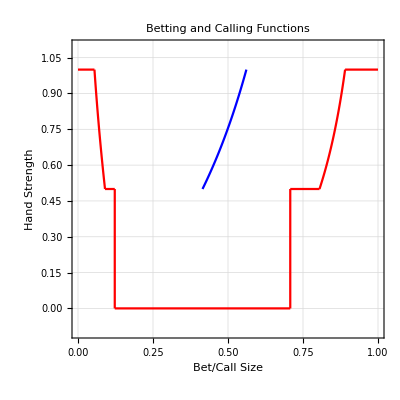

```mathematica
(*Define parameters and common settings*)
params={L->0.5,U->1};
plotRange={{0,1},{-0.1,1.1*(U/. params)}};

nbDir=DirectoryName[NotebookFileName[]]

(*Define the individual segments of the betting function*)
betColor=Red;
betFunction={ParametricPlot[{x,U/. params},{x,0,x0/. LimitSol/. params},PlotStyle->betColor,PlotRange->plotRange],ParametricPlot[{b[s,L,U]/. params,s},{s,L/. params,U/. params},PlotStyle->betColor,PlotRange->plotRange],ParametricPlot[{x,L/. params},{x,x1/. LimitSol/. params,x2/. LimitSol/. params},PlotStyle->betColor,PlotRange->plotRange],ParametricPlot[{x2/.LimitSol/.params,y},{y,0,L/.params},PlotStyle->betColor,PlotRange->plotRange],ParametricPlot[{x,0},{x,x2/. LimitSol/. params,x3/. LimitSol/. params},PlotStyle->betColor,PlotRange->plotRange],ParametricPlot[{x3/.LimitSol/.params,y},{y,0,L/.params},PlotStyle->betColor,PlotRange->plotRange],ParametricPlot[{x,L/. params},{x,x3/. LimitSol/. params,x4/. LimitSol/. params},PlotStyle->betColor,PlotRange->plotRange],ParametricPlot[{v[s,L,U]/. params,s},{s,L/. params,U/. params},PlotStyle->betColor,PlotRange->plotRange],ParametricPlot[{x,U/. params},{x,x5/. LimitSol/. params,1},PlotStyle->betColor,PlotRange->plotRange]};
(*Extract data points from betFunction*)
betFunctionData=Table[Cases[Normal[betFunction[[i]]],Line[pts_]:>pts,Infinity],{i,Length[betFunction]}];
(*Export the data to a JSON file*)
Export[FileNameJoin[{nbDir,"betFunction.json"}],betFunctionData,"JSON"];

(*Add the calling function*)
callColor=Blue;
callFunction={ParametricPlot[{c[s,L,U]/. params,s},{s,L/. params,U/. params},PlotStyle->callColor,PlotRange->plotRange]};
callFunctionData=Table[Cases[Normal[callFunction[[i]]],Line[pts_]:>pts,Infinity],{i,Length[callFunction]}];
Export[FileNameJoin[{nbDir,"callFunction.json"}],callFunctionData,"JSON"];

(*Write metadata to a JSON file*)
metadata=<|"Parameters"-><|"L"->(L/. params),"U"->(U/. params)|>,"Description"->"Metadata for betting and calling functions","GeneratedOn"->DateString[]|>;
Export[FileNameJoin[{nbDir,"metadata.json"}],metadata,"JSON"];

allPlots=Union[betFunction,callFunction];

(*Show the combined plot*)
Show[allPlots,PlotRange->plotRange,AxesLabel->{"Bet/Call Size","Hand Strength"},PlotLabel->"Betting and Calling Functions",AspectRatio->1,GridLines->Automatic,Frame->True,FrameLabel->{"Bet/Call Size","Hand Strength"},PlotStyle->{betColor,callColor}]
```